Read in data for 2D HO, for <x> and <y>

```mathematica
DHKkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\DHK_k.5.out",Real];
DHKk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\DHK_k1.0.out",Real];
DHKk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\DHK_k2.0.out",Real];

HWDkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\HWD_k.5.out",Real];
HWDk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\HWD_k1.0.out",Real];
HWDk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\HWD_k2.0.out",Real];

aMQCSPkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\AMQC_SP_k.5.out",Real];
aMQCSPk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\AMQC_SP_k1.0.out",Real];
aMQCSPk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\AMQC_SP_k2.0.out",Real];

LSCxkp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCx_k.5.out",Real];LSCxk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCx_k1.0.out",Real];
LSCxk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCx_k2.0.out",Real];

LSCykp5data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCy_k.5.out",Real];LSCyk1data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCy_k1.0.out",Real];
LSCyk2data=ReadList["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\LSCy_k2.0.out",Real];
```

Arrange <x> and <y> for plotting.

```mathematica
dhkx={Table[{DHKkp5data[[5*i-4]],DHKkp5data[[5*i-3]]},{i,1,Length[DHKkp5data]/5}],Table[{DHKk1data[[5*i-4]],DHKk1data[[5*i-3]]},{i,1,Length[DHKk1data]/5}],Table[{DHKk2data[[5*i-4]],DHKk2data[[5*i-3]]},{i,1,Length[DHKk2data]/5}]};
dhky={Table[{DHKkp5data[[5*i-4]],DHKkp5data[[5*i-1]]},{i,1,Length[DHKkp5data]/5}],Table[{DHKk1data[[5*i-4]],DHKk1data[[5*i-1]]},{i,1,Length[DHKk1data]/5}],Table[{DHKk2data[[5*i-4]],DHKk2data[[5*i-1]]},{i,1,Length[DHKk2data]/5}]};hwdx={Table[{HWDkp5data[[5*i-4]],HWDkp5data[[5*i-3]]},{i,1,Length[HWDkp5data]/5}],Table[{HWDk1data[[5*i-4]],HWDk1data[[5*i-3]]},{i,1,Length[HWDk1data]/5}],Table[{HWDk2data[[5*i-4]],HWDk2data[[5*i-3]]},{i,1,Length[HWDk2data]/5}]};
hwdy={Table[{HWDkp5data[[5*i-4]],HWDkp5data[[5*i-1]]},{i,1,Length[HWDkp5data]/5}],Table[{HWDk1data[[5*i-4]],HWDk1data[[5*i-1]]},{i,1,Length[HWDk1data]/5}],Table[{HWDk2data[[5*i-4]],HWDk2data[[5*i-1]]},{i,1,Length[HWDk2data]/5}]};
amqcspx={Table[{aMQCSPkp5data[[3*i-2]],aMQCSPkp5data[[3*i-1]]},{i,1,Length[aMQCSPkp5data]/3}],Table[{aMQCSPk1data[[3*i-2]],aMQCSPk1data[[3*i-1]]},{i,1,Length[aMQCSPk1data]/3}],Table[{aMQCSPk2data[[3*i-2]],aMQCSPk2data[[3*i-1]]},{i,1,Length[aMQCSPk2data]/3}]};
lscx={Table[{LSCxkp5data[[2*i-1]],LSCxkp5data[[2*i]]},{i,1,Length[LSCxkp5data]/2}],Table[{LSCxk1data[[2*i-1]],LSCxk1data[[2*i]]},{i,1,Length[LSCxk1data]/2}],Table[{LSCxk2data[[2*i-1]],LSCxk2data[[2*i]]},{i,1,Length[LSCxk2data]/2}]};
lscy={Table[{LSCykp5data[[2*i-1]],LSCykp5data[[2*i]]},{i,1,Length[LSCykp5data]/2}],Table[{LSCyk1data[[2*i-1]],LSCyk1data[[2*i]]},{i,1,Length[LSCyk1data]/2}],Table[{LSCyk2data[[2*i-1]],LSCyk2data[[2*i]]},{i,1,Length[LSCyk2data]/2}]};
```

#### Make plots of all three σ’s for all four models

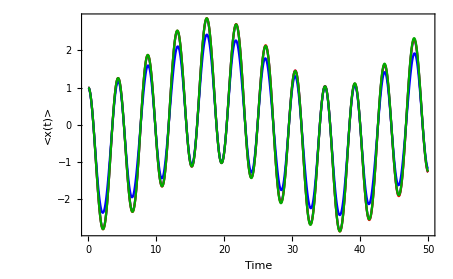

```mathematica
ListLinePlot[{dhkx[[3]],hwdx[[3]],amqcspx[[3]],lscx[[3]]},PlotStyle->{Blue,Red,Blue,Darker[Green]},PlotRange->Full,GridLines->None,FrameLabel->{"Time","<x(t)>"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]]
```

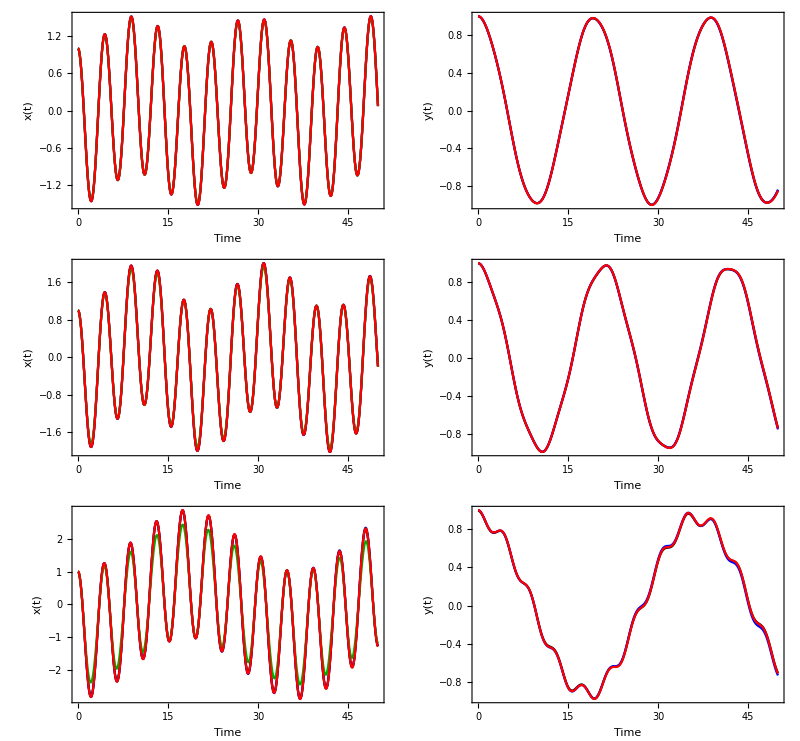

```mathematica
plot1=Legended[GraphicsGrid[Table[{ListLinePlot[{dhkx[[j]],lscx[[j]],amqcspx[[j]],hwdx[[j]]},PlotStyle->{Black,Darker[Blue],Darker[Green],Red},PlotRange->Automatic,GridLines->None,FrameLabel->{"Time","x(t)"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]],ListLinePlot[{dhky[[j]],lscy[[j]],hwdy[[j]]},PlotStyle->{Black,Blue,Red},PlotRange->Automatic,GridLines->None,FrameLabel->{"Time","y(t)"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],PlotRangePadding->0,BaseStyle->Directive[16,Black],FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black]]},{j,1,3}],Spacings->0],Placed[LineLegend[{Black,Darker[Blue],Darker[Green],Red},{"DHK","LSC","aMQC-SP","AHWD"},LegendLayout->"Row"],Top]]
```

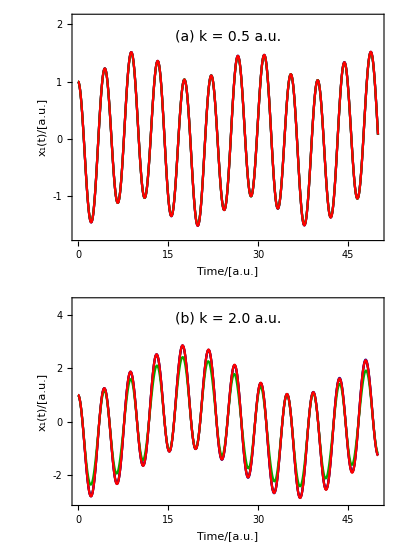

```mathematica
plot1=Legended[GraphicsColumn[{ListLinePlot[{dhkx[[1]],lscx[[1]],amqcspx[[1]],hwdx[[1]]},PlotStyle->{Black,Darker[Blue],Darker[Green],Red},PlotRange->{{0,50},{-1.7,2.1}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-1,0,1,2},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],ImagePadding->{{Automatic, 5}, {60,Automatic}},Epilog->Text[Style["(a) k = 0.5 a.u.",14],Scaled[{0.5,0.90}]]],(*ListLinePlot[{dhkx[[2]],lscx[[2]],amqcspx[[2]],hwdx[[2]]},PlotStyle->{Black,Darker[Blue],Darker[Green],Red},PlotRange->{{0,50},{-2.2,2.9}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-1,0,1,2},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],ImagePadding->{{Automatic, 5}, {60,Automatic}},Epilog->Text[Style["(b) k = 1.0 a.u.",14],Scaled[{0.5,0.90}]]],*)ListLinePlot[{dhkx[[3]],lscx[[3]],amqcspx[[3]],hwdx[[3]]},PlotStyle->{Black,Darker[Blue],Darker[Green],Red},PlotRange->{{0,50},{-3,4.5}},GridLines->None,FrameLabel->{"Time/[a.u.]","x_1(t)/[a.u.]"},Frame->True,GridLinesStyle->Directive[Gray, Thickness[10^-6]],BaseStyle->Directive[16,Black],FrameTicks->{{{-2,0,2,4},None},{Automatic,None}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,14],Axes->False,LabelStyle->Directive[16,Black],Epilog->Text[Style["(b) k = 2.0 a.u.",14],Scaled[{0.5,0.90}]]]},Spacings->0],Placed[LineLegend[{Black,Darker[Blue],Darker[Green],Red},{"DHK","LSC","aMQC-SP","AHWD"},LegendLayout->"Row"],Top]]
```

```mathematica
Export["C:\\Users\\shrey\\Documents\\Lab\\SC-IVR Code\\2D_HO\\2D_HO.pdf",plot1]
```

C:\Users\shrey\Documents\Lab\SC-IVR Code\2D_HO\2D_HO.pdf